```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]]
```

```mathematica
(*This has no evaluation Step*)
```

#### (* Here are the different operators *)

```mathematica
operatorHadamard = QuantumMatrixOperation["Hadamard"];
```

```mathematica
operatorRotate = QuantumMatrixOperation[{"RotZ",Pi/4}];
```

```mathematica
operatorCNOT = QuantumMatrixOperation["CNOT"];
```

```mathematica
operatorPauliZ = QuantumMatrixOperation["SigmaZ"];
```

```mathematica
operatorPauliY = QuantumMatrixOperation["SigmaY"];
```

```mathematica
operatorPauliX = QuantumMatrixOperation["SigmaX"];
```

```mathematica
operatorSqrtNOT = QuantumMatrixOperation[1/2*{{1+I,1-I},{1-I,1+I}}];
```

```mathematica
operatorFourier = QuantumMatrixOperation[{"Fourier",2}];
```

#### (* states for test *)

```mathematica
states ={QuantumFiniteDimensionalState[{{1,0}}],QuantumFiniteDimensionalState[{{0,1}}],QuantumFiniteDimensionalState[{{1,0}}]};
```

#### (* fixing normalization *)

```mathematica
fixStupidity[expression_]:=((expression)//.{Sqrt[x_]->x,Power[x_,Rational[m_Integer,n_Integer]]->x,Power[x_,Rational[-m_Integer,n_Integer]]->1/x})
```

#### (* generating entanglement tools *)

```mathematica
generateEntangledState[]:=QuantumFiniteDimensionalState[{"PhiPlus"}]
```

```mathematica
entangledpair = generateEntangledState[];
```

```mathematica
entangledMeasurement = QuantumMeasurement["Observable"-> "SigmaX"];
```

(* create QFDS, of state qubit (j+1) and entangled states *)
(* apply CNOT on state qubit and first entangled qubit *)
(* apply Hadamard on state qubit *)
(* measure state qubit and second entangled qubit *)

```mathematica
entangledThreeState[pair_,states_,j_Integer]:=
QuantumFiniteDimensionalState[fixStupidity[{Normal[states⟦j+1⟧["StateVector"]],Normal[pair["StateVector"]]}]]/;j≠Length[states]

entangledThreeState[pair_,states_,j_Integer]:=
QuantumFiniteDimensionalState[fixStupidity[{Normal[states⟦1⟧["StateVector"]],Normal[pair["StateVector"]]}]]/;j===Length[states]
```

```mathematica
entangledThreeState[entangledpair,states,3]
```

QuantumFiniteDimensionalState[…]

```mathematica
chooseTeleportationOperation[pair_,states_,j_Integer]:=
Flatten[{QuantumEvaluate[{1}-> entangledMeasurement,
QuantumEvaluate[{1}-> operatorHadamard,QuantumEvaluate[{1,2}-> operatorCNOT,entangledThreeState[pair,states,j]]]],QuantumEvaluate[{2}-> entangledMeasurement,QuantumEvaluate[{1,2}-> operatorCNOT,entangledThreeState[pair,states,j]]]
}]
```

```mathematica
chooseTeleportationOperation[generateEntangledState[],states,2]
```

{1,1}

```mathematica
QuantumEvaluate[{1}-> entangledMeasurement,QuantumFiniteDimensionalState[…]]
```

{-1}

```mathematica
operators = {operatorHadamard,operatorPauliX,operatorPauliY,operatorPauliZ};
```

```mathematica
applyControlOperation[pair_,states_,j_Integer,operators_]:=
Module[{answer=chooseTeleportationOperation[pair,states,j]},
Which[
answer==={-1,-1},
QuantumEvaluate[{1}-> operators⟦1⟧,states⟦j⟧],
answer==={-1,1},
QuantumEvaluate[{1}-> operators⟦2⟧,states⟦j⟧],
answer==={1,-1},
QuantumEvaluate[{1}-> operators⟦3⟧,states⟦j⟧],
answer==={1,1},
QuantumEvaluate[{1}-> operators⟦4⟧,states⟦j⟧]]]
```

```mathematica
applyControlOperation[generateEntangledState[],states,1,operators]
```

QuantumFiniteDimensionalState[…]

(* create new cell based on new control qubit, teleported state qubit, and both of them put through an operator *)

```mathematica
createNewCell[j_Integer,states_,pair_,operators_]:= 
QuantumFiniteDimensionalState[fixStupidity[
{Normal[applyControlOperation[pair,states,j,operators]["StateVector"]]}]]
```

```mathematica
(* What Airty 2 operations do in terms of mixing things up so you can't separate individual qubits after, this was applying final operation of operatorCNOT followed by operatorFourier *)
```

```mathematica
QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumFiniteDimensionalState[…]["StateVector"]]}]]
```

QuantumFiniteDimensionalState[…]

```mathematica
QuantumPartialTr[QuantumFiniteDimensionalState[…],{1}]
```

QuantumFiniteDimensionalState[…]

```mathematica
QuantumFiniteDimensionalState[…];
```

(* repeat for all *)

```mathematica
nextState[pair_,states_,operators_]:= createNewCell[#,states,pair,operators]&/@Range[Length[states]]
```

```mathematica
allStates[pair_,states_,operators_,n_Integer]:= NestList[nextState[pair,#,operators]&,states,n]
```

```mathematica
allStates[generateEntangledState[],states,5];
```

```mathematica
(* in CA, finding disorder and randomness from initial structure is a surprise, in QCA finding order is a surprise? *)
```

#### (*Data Analysis*)

```mathematica
separateStates[states_]:= Map[Normal[#["StateVector"]]&,states]
separateAllStates[states_]:= separateStates[#]&/@states
```

```mathematica
separateAllStates[allStates[generateEntangledState[],states,20]]
```

{{{1,0},{0,1},{1,0}},{{0,ⅈ},{0,1},{-1,0}},{{1,0},{1/(√2),-1/(√2)},{0,-ⅈ}},{{0,1},{ⅈ/(√2),ⅈ/(√2)},{-ⅈ/(√2),ⅈ/(√2)}},{{1/(√2),-1/(√2)},{-ⅈ/(√2),ⅈ/(√2)},{ⅈ/(√2),-ⅈ/(√2)}},{{0,1},{0,-ⅈ},{-1/(√2),-1/(√2)}},{{1,0},{-ⅈ/(√2),ⅈ/(√2)},{-1/(√2),-1/(√2)}},{{-1,0},{0,-ⅈ},{1/(√2),-1/(√2)}},{{0,-ⅈ},{0,-ⅈ},{0,1}},{{-1,0},{-1,0},{-ⅈ,0}},{{1,0},{-1/(√2),-1/(√2)},{ⅈ,0}},{{1/(√2),1/(√2)},{-1,0},{-ⅈ,0}},{{1,0},{1,0},{ⅈ,0}},{{-1,0},{-1,0},{ⅈ/(√2),ⅈ/(√2)}},{{1,0},{0,-ⅈ},{-ⅈ/(√2),ⅈ/(√2)}},{{0,1},{-1,0},{ⅈ/(√2),ⅈ/(√2)}},{{0,1},{-1/(√2),-1/(√2)},{ⅈ/(√2),ⅈ/(√2)}},{{1/(√2),-1/(√2)},{1/(√2),-1/(√2)},{ⅈ/(√2),ⅈ/(√2)}},{{-1/(√2),1/(√2)},{ⅈ/(√2),ⅈ/(√2)},{1/(√2),-1/(√2)}},{{1/(√2),1/(√2)},{1/(√2),-1/(√2)},{-1/(√2),1/(√2)}},{{-1/(√2),1/(√2)},{-1/(√2),1/(√2)},{-ⅈ/(√2),-ⅈ/(√2)}}}

```mathematica
countEachState[states_]:= Counts[Flatten[separateAllStates[states],1]]
```

```mathematica
showCountEachState[states_]:= BarChart[Sort[countEachState[states]], ChartLabels->Automatic,AxesLabel->Automatic, BarOrigin-> Left, ImageSize->Large]
```

```mathematica
howMuchOfEachState[states_]:= Length[countEachState[states]]
```

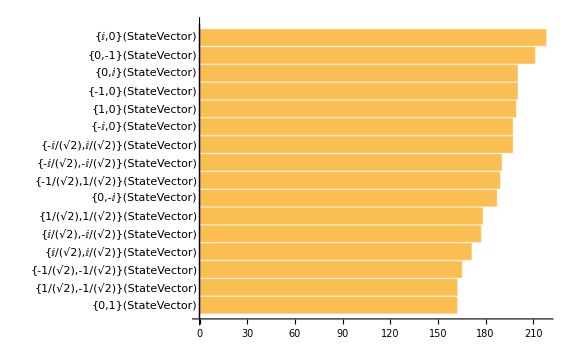

```mathematica
showCountEachState[separateAllStates[allStates[generateEntangledState[],states,1000]]]
```

#### (* Visualization *)

```mathematica
getColour[com_]:= RGBColor[N[Re[com],10],0,N[Im[com],10]]/;Re[com]≥ 0&&Im[com]≥0
getColour[com_]:= Blend[{ColorNegate[RGBColor[Abs[N[Re[com],10]],0,0]],RGBColor[0,0,N[Im[com],10]]}]/;Re[com]≤ 0&&Im[com]≥0
getColour[com_]:= Blend[{RGBColor[Abs[N[Re[com],10]],0,0],ColorNegate[RGBColor[0,0,N[Im[com],10]]]}]/;Re[com]≥ 0&&Im[com]≤0
getColour[com_]:= Blend[{ColorNegate[RGBColor[Abs[N[Re[com],10]],0,0]],ColorNegate[RGBColor[0,0,N[Im[com],10]]]}]/;Re[com]≤ 0&&Im[com]≤0
```

```mathematica
colourQubit[qubit_]:= {getColour[qubit⟦1⟧],getColour[qubit⟦2⟧]}
```

```mathematica
colourQubit[{1,0}]
```

{RGBColor[1., 0, 0],RGBColor[0, 0, 0]}

```mathematica
colourQubit[{0,I}]
```

{RGBColor[0, 0, 0],RGBColor[0, 0, 1.]}

```mathematica
colourQubit[{-1,0}]
```

{RGBColor[0., 0.5, 0.5],RGBColor[0, 0, 0]}

```mathematica
colourQubit[{0,-I}]
```

{RGBColor[0, 0, 0],RGBColor[0.5, 0.5, 0.5]}

```mathematica
colourState[state_]:=Map[colourQubit,state]
```

```mathematica
colourAll[allstates_]:=Map[colourState, allstates]
```

```mathematica
showQubit[qubit_]:= Annotation[Rotate[ArrayPlot[{colourQubit[qubit]},Frame-> False,PlotRangePadding->None, ImageSize->Small],3Pi/2],qubit,"Mouse"]
```

```mathematica
showQubit[{1,0}];
```

```mathematica
showState[state_]:=Map[showQubit,state]
```

```mathematica
showAll[allState_]:= GraphicsGrid[Map[showState,allState],ItemAspectRatio->2]
```

```mathematica
initialState[n_Integer]:=Join[Table[QuantumFiniteDimensionalState[{{1,0}}],(n-1)/2],{QuantumFiniteDimensionalState[{{0,1}}]},Table[QuantumFiniteDimensionalState[{{1,0}}],(n-1)/2]]
```

```mathematica
initialState[5]
```

{QuantumFiniteDimensionalState[…],QuantumFiniteDimensionalState[…],QuantumFiniteDimensionalState[…],QuantumFiniteDimensionalState[…],QuantumFiniteDimensionalState[…]}

```mathematica
QuantumCellularAutomata[operators_,steps_Integer]:= showAll[separateAllStates[allStates[generateEntangledState[],initialState[2*steps + 1],operators,steps]]]
```

```mathematica
QuantumCellularAutomata[operators,50]
```

-Graphics-

```mathematica
QuantumCellularAutomata[operators,10]
```

-Graphics-

```mathematica
Dynamic[MouseAnnotation[]]
```

#### (* Physics Applications *)

```mathematica
onequbit = QuantumFiniteDimensionalState[{{1,0}}]
```

QuantumFiniteDimensionalState[…]

```mathematica
$hbar = 1;
```

```mathematica
$epsilon = 1;
```

```mathematica
$t = 1;
```

```mathematica
matrixHamiltonian1 = {{$epsilon,$t},{$t,-$epsilon}}
```

{{1,1},{1,-1}}

```mathematica
operatorU[t_,hamiltonian_] := QuantumMatrixOperation[N[Cos[hamiltonian*t/$hbar],10]- I*N[Sin[hamiltonian*t/$hbar],10]]
```

```mathematica
operatorU[0, matrixHamiltonian1]
```

QuantumMatrixOperation[…]

```mathematica
qubitEvolve[t_,operator_,initialqubit_,hamiltonian_]:=QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1}-> operator[t,hamiltonian],initialqubit]["StateVector"]]}]]
```

```mathematica
qubitEvolve[0,operatorU,onequbit, matrixHamiltonian1]
```

QuantumFiniteDimensionalState[…]

```mathematica
qubitEvolution[operator_,initialqubit_,hamiltonian_]:=qubitEvolve[#,operator,initialqubit,hamiltonian]&/@Range[0,4*Pi,0.5]
```

```mathematica
qubitEvolution[operatorU,onequbit, $epsilon,$t];
```

```mathematica
showQubitEvolution[operator_,initialqubit_,hamiltonian_]:= GraphicsGrid[{showState[separateStates[qubitEvolution[operator,initialqubit,hamiltonian]]]},ItemAspectRatio->2]
```

```mathematica
showQubitEvolution[operatorU,onequbit, $epsilon,$t]
```

-Graphics-

```mathematica
(* increase epsilon and decrease t*)
```

```mathematica
tsmall = 0.5;
epsilonbig= 2;
```

```mathematica
showQubitEvolution[operatorU,onequbit,$epsilon,tsmall]
```

-Graphics-

```mathematica
showQubitEvolution[operatorU,onequbit,epsilonbig,$t]
```

-Graphics-

```mathematica
Dynamic[MouseAnnotation[]]
```

```mathematica
oneMatrix = {{1,0},{0,0}}
```

{{1,0},{0,0}}

```mathematica
operatorDensityMatrix = QuantumMatrixOperation[{{1,0},{0,0}}]
```

QuantumMatrixOperation[…]

```mathematica
(*densityMatrix[qubit_]:= QuantumEvaluate[{1}-> QuantumMatrixOperation[QuantumEvaluate[{1}-> operatorDensityMatrix,qubit]["MatrixRepresentation"]],QuantumFiniteDimensionalState[fixStupidity[{{Conjugate[First[Normal[qubit["StateVector"]]]],Conjugate[Last[Normal[qubit["StateVector"]]]]}}]]]*)
```

```mathematica
Norm[Normal[QuantumFiniteDimensionalState[…]["StateVector"]]]
```

1.

```mathematica
densityMatrix[qubit_]:= Normal[qubit["StateVector"]]*oneMatrix*{Conjugate[First[Normal[qubit["StateVector"]]]],Conjugate[Last[Normal[qubit["StateVector"]]]]}
```

```mathematica
densityMatrix[QuantumFiniteDimensionalState[…]]
```

{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
allDensityMatrix[operator_,qubit_,hamiltonian_]:=densityMatrix[#]&/@qubitEvolution[operator,qubit,hamiltonian]
```

```mathematica
allDensityMatrix[operatorU,onequbit,matrixHamiltonian1]
```

{{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}},{{0.5+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}}

```mathematica
{showQubitEvolution[operatorU,#,$epsilon,$t]}&/@initialState[5];
```

#### Precession

```mathematica
g= 9.81;
q = 1.602*10^-19;
m = 9.11*10^-31;
gamma = g*q/2*m;
omega = 1;
B = 1;
```

```mathematica
operatorPrecession[t_] := QuantumMatrixOperation[{{N[Cos[omega*t],10]+ I*N[Sin[omega*t]],0},{N[Cos[omega*t],10]- I*N[Sin[omega*t]],0}}]
```

```mathematica
operatorPrecession[1]
```

QuantumMatrixOperation[…]

```mathematica
qubitEvolveP[t_,operator_,initialqubit_]:=QuantumEvaluate[{1}->operatorHadamard,QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1}-> operator[t],initialqubit]["StateVector"]]}]]]
```

```mathematica
qubitEvolveP[1,operatorPrecession,onequbit]
```

QuantumFiniteDimensionalState[…]

```mathematica
qubitEvolutionP[operator_,initialqubit_]:=qubitEvolveP[#,operator,initialqubit]&/@Range[0,25,0.5]
```

```mathematica
qubitEvolutionP[operatorPrecession,onequbit];
```

```mathematica
showQubitEvolutionP[operator_,initialqubit_]:= GraphicsGrid[{showState[separateStates[qubitEvolutionP[operator,initialqubit]]]},ItemAspectRatio->2]
```

```mathematica
showQubitEvolutionP[operatorPrecession,onequbit]
```

-Graphics-

```mathematica
Dynamic[MouseAnnotation[]]
```

```mathematica
omega = 0.5;
```

```mathematica
showQubitEvolutionP[operatorPrecession,onequbit]
```

-Graphics-

```mathematica
omega = 2;
showQubitEvolutionP[operatorPrecession,onequbit]
```

-Graphics-

#### Coupled 2 Two State Systems

```mathematica
twoqubits = QuantumFiniteDimensionalState[{{1,0},{1,0}}]
```

QuantumFiniteDimensionalState[…]

```mathematica
a=1;
b=1;
c=1;
```

```mathematica
matrixHamiltonian2 ={{a,b-c,0,0},{b+c,-a,0,0},{0,0,a,-b},{0,0,b+c,-a}};
```

```mathematica
operatorU2[t_,hamiltonian_]:=QuantumMatrixOperation[N[Cos[hamiltonian*t/$hbar],10]- I*N[Sin[hamiltonian*t/$hbar],10]]
```

```mathematica
qubitEvolve2[t_,operator_,hamiltonian_,initialqubit_]:= QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1,2}-> operator[t,hamiltonian],initialqubit]["StateVector"]]}]]
```

```mathematica
qubitEvolution2[operator_,initialqubit_]:=qubitEvolve2[#,operator,matrixHamiltonian2,initialqubit]&/@Range[0,5,0.5]
```

```mathematica
qubitEvolution2[operatorU2,twoqubits]
```

```mathematica
separateStates[qubitEvolution2[operatorU2,twoqubits]]
```

{{0.5+0. ⅈ,0.5+0. ⅈ,0.5+0. ⅈ,0.5+0. ⅈ},{0.438791-0.239713 ⅈ,0.270151-0.420735 ⅈ,0.5+0. ⅈ,0.5+0. ⅈ},{0.270151-0.420735 ⅈ,-0.208073-0.454649 ⅈ,0.5+0. ⅈ,0.5+0. ⅈ},{0.0353686-0.498747 ⅈ,-0.494996-0.07056 ⅈ,0.5+0. ⅈ,0.5+0. ⅈ},{-0.208073-0.454649 ⅈ,-0.326822+0.378401 ⅈ,0.5+0. ⅈ,0.5+0. ⅈ},{-0.400572-0.299236 ⅈ,0.141831+0.479462 ⅈ,0.5+0. ⅈ,0.5+0. ⅈ},{-0.494996-0.07056 ⅈ,0.480085+0.139708 ⅈ,0.5+0. ⅈ,0.5+0. ⅈ},{-0.468228+0.175392 ⅈ,0.376951-0.328493 ⅈ,0.5+0. ⅈ,0.5+0. ⅈ},{-0.326822+0.378401 ⅈ,-0.07275-0.494679 ⅈ,0.5+0. ⅈ,0.5+0. ⅈ},{-0.105398+0.488765 ⅈ,-0.455565-0.206059 ⅈ,0.5+0. ⅈ,0.5+0. ⅈ},{0.141831+0.479462 ⅈ,-0.419536+0.272011 ⅈ,0.5+0. ⅈ,0.5+0. ⅈ}}

```mathematica
colourQubit2[qubit_]:= {getColour[qubit⟦1⟧],getColour[qubit⟦2⟧],getColour[qubit⟦3⟧],getColour[qubit⟦4⟧]}
```

```mathematica
colourState2[state_]:=Map[colourQubit2,state]
```

```mathematica
showQubit2[qubit_]:= Annotation[Rotate[ArrayPlot[{colourQubit2[qubit]},Frame-> False,PlotRangePadding->None, ImageSize->Small],3Pi/2],qubit,"Mouse"]
```

```mathematica
showState2[state_]:=Map[showQubit2,state]
```

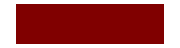
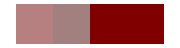
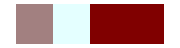
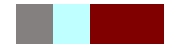
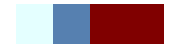
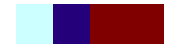
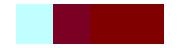
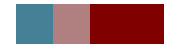

```mathematica
showState2[separateStates[qubitEvolution2[operatorU2,twoqubits]]]
```

```mathematica
showQubitEvolution2[operator_,initialqubit_]:= GraphicsGrid[{showState2[separateStates[qubitEvolution2[operator,initialqubit]]]},ItemAspectRatio->4]
```

```mathematica
showQubitEvolution2[operatorU2,twoqubits]
```

-Graphics-

```mathematica
ClearAll[a,b,c,d,e,f]
```

```mathematica
sigmaX = {{0,1},{1,0}};
sigmaY={{0,-I},{I,0}};
sigmaZ = {{1,0},{0,-1}};
(a*sigmaX*b*sigmaX) + (c*sigmaY*d*sigmaY) + (e*sigmaZ*f*sigmaZ)
```

{{e f,a b-c d},{a b-c d,e f}}

#### Heisenberg Spin Chains (NN interactions)

```mathematica
hamiltonianTimeX[t_]:= QuantumMatrixOperation[N[Cos[{{0,1},{1,0}}*t/$hbar],10]- I*N[Sin[{{0,1},{1,0}}*t/$hbar],10]]
```

```mathematica
hamiltonianTimeY[t_]:= QuantumMatrixOperation[N[Cos[{{0,-I},{I,0}}*t/$hbar],10]- I*N[Sin[{{0,-I},{I,0}}*t/$hbar],10]]
```

```mathematica
hamiltonianTimeZ[t_]:= QuantumMatrixOperation[N[Cos[{{1,0},{0,-1}}*t/$hbar],10]- I*N[Sin[{{1,0},{0,-1}}*t/$hbar],10]]
```

```mathematica
nextQubitH[t_,j_Integer,states_]:=Normal[QuantumFiniteDimensionalState[fixStupidity[{(Normal[QuantumEvaluate[{j}-> hamiltonianTimeX[t],states]["StateVector"]]*Normal[QuantumEvaluate[{j+1}-> hamiltonianTimeX[t],states]["StateVector"]])+
(Normal[QuantumEvaluate[{j}-> hamiltonianTimeY[t],states]["StateVector"]]*Normal[QuantumEvaluate[{j+1}-> hamiltonianTimeY[t],states]["StateVector"]])+
(Normal[QuantumEvaluate[{j}-> hamiltonianTimeZ[t],states]["StateVector"]]*Normal[QuantumEvaluate[{j+1}-> hamiltonianTimeZ[t],states]["StateVector"]])}]]["StateVector"]]/;j≠ Log[2,Length[Normal[states["StateVector"]]]]

nextQubitH[t_,j_Integer,states_]:=Normal[QuantumFiniteDimensionalState[fixStupidity[{(Normal[QuantumEvaluate[{j}-> hamiltonianTimeX[t],states]["StateVector"]]*Normal[QuantumEvaluate[{1}-> hamiltonianTimeX[t],states]["StateVector"]])+
(Normal[QuantumEvaluate[{j}-> hamiltonianTimeY[t],states]["StateVector"]]*Normal[QuantumEvaluate[{1}-> hamiltonianTimeY[t],states]["StateVector"]])+
(Normal[QuantumEvaluate[{j}-> hamiltonianTimeZ[t],states]["StateVector"]]*Normal[QuantumEvaluate[{1}-> hamiltonianTimeZ[t],states]["StateVector"]])}]]["StateVector"]]/;j=== Log[2,Length[Normal[states["StateVector"]]]]
```

```mathematica
nextQubitH[1,1,QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}]]
```

{0.86724166-0.49788745 ⅈ,0,0,0,0,0,0,0}

```mathematica
nextStateH[t_,states_]:= Total[nextQubitH[t,#,states]&/@Range[Log[2,Length[Normal[states["StateVector"]]]]]]
```

```mathematica
nextStateH[3,QuantumFiniteDimensionalState[{{1,0},{0,1},{1,0}}]]
```

{0,0,2.995575+0.09397398 ⅈ,0,0,0,0,0}

```mathematica
fullEvolutionH[states_,timeduration_,timestep_]:= Normal[QuantumFiniteDimensionalState[fixStupidity[{nextStateH[#,states]}]]["StateVector"]]&/@Range[0,timeduration,timestep]
```

```mathematica
fullEvolutionH[QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],10,1]
```

{{1.,0,0,0,0,0,0,0},{0.86724166-0.49788745 ⅈ,0,0,0,0,0,0,0},{0.8717202+0.490004 ⅈ,0,0,0,0,0,0,0},{0.9955747+0.09397398 ⅈ,0,0,0,0,0,0,0},{0.8823-0.4707 ⅈ,0,0,0,0,0,0,0},{0.9055+0.4243 ⅈ,0,0,0,0,0,0,0},{0.9827+0.1854 ⅈ,0,0,0,0,0,0,0},{0.907-0.421 ⅈ,0,0,0,0,0,0,0},{0.96+0.27 ⅈ,0,0,0,0,0,0,0},{1.+0.3 ⅈ,0,0,0,0,0,0,0},{0.9-0.4 ⅈ,0,0,0,0,0,0,0}}

```mathematica
colourNQubit[qubit_]:= getColour[qubit⟦#⟧]&/@Range[Length[qubit]]
```

```mathematica
colourNQubit[{0.8672416565683119731`8.507188359954093-0.4978874462292155748`8.507188359954093 ⅈ,0,0,0,0,0,0,0},8]
```

{RGBColor[0.933620828284156, 0.5, 0.5],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]}

```mathematica
showHeisenbergEvolution[states_,timeduration_,timestep_]:= colourNQubit[#]&/@fullEvolutionH[states,timeduration,timestep]
```

```mathematica
showHeisenbergEvolution[QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],10,1]
```

{{RGBColor[1., 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]},{RGBColor[0.933620828284156, 0.5, 0.5],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]},{RGBColor[0.8717201845798141116, 0, 0.4900039997756496024],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]},{RGBColor[0.9955746535529563197, 0, 0.0939739815210093059],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]},{RGBColor[0.9411476651214199, 0.5, 0.5],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]},{RGBColor[0.9055081225423378812, 0, 0.4243289290277654438],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]},{RGBColor[0.9826618615383034, 0, 0.1854067579083250054],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]},{RGBColor[0.9536219253752647, 0.5, 0.5],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]},{RGBColor[0.9639069635589414269, 0, 0.2662393013861431466],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]},{RGBColor[0.9623890196983417031, 0, 0.2716751272458795876],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]},{RGBColor[0.9675287053119634, 0.5, 0.5],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0],RGBColor[0, 0, 0]}}